# CEPC Higgs Precision

(Starting date: Sep. 2014)
(Dated: Sep. 11th,2015)
(Updated: Sep. 2017 for CEPC CDR）
(Updated: Oct. 2017 for CEPC CDR, with covariance matrix)
(Updated: Jul. 2018 for CEPC CDR, with sub-fits for sub regions for total width)
(Updated: Sep. 2018 for CEPC CDR, with corrected definition of covariance matrix)
(Updated: Sep. 2018 for CEPC CDR, with sub-fits for sub regions for total width)
This code is used to determine projected Higgs precision achievable at Circular-Elector-Positron-Collider. 

A proper definition of projected precision has many physical requirements and can be defined in several different ways. The definition of precision on each parameter is using profiled-likelihood. Technically the definition is as follows, 
a) define a likelihood function;
a.a) here we take the probability P as -2Log[P]=χ^2 up to proper normalization;
a.b) χ^2 is defined as sum of (obs.-exp.)^2/(σ^2)_(Obs.), where obs. and exp. stands for observed and expected quantity and σ stands for the standard deviation;
b) find the allowed 1-sigma regions for a (set of) given parameter(s) κ(s);
b.a) this is equivalent to finding the largest range of  κ(s) that follow Δχ^2=χ^2-χ_min^2≤1;
b.b) “profiled” means while attempting to find such range, all the other parameters are allowed to vary freely within physical boundaries to minimize Δχ^2.
This program uses very simple linear regression method in finding such intervals. The efficiency of such algorithm decreases drastically for constrained fits with complex boundary conditions.

This fitting provides us guidance in prioritizing channels to study for the purpose of precision Higgs physics. Such guidance is indirect, only reveals itself via studying. 

Please consult Zhen Liu (zliuphys@umd.edu) for detailed explanation.

## PreCDR

## SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

## CEPC

This is the CEPC fitting program.
For simplicity, I removed many other components involving interfacing with HL-LHC/ILC measurements, other tested fits, etc.

7p and 10p stands for 7-parameter and 10-parameter;
“MD” stands for Model-dependent;
“MI” stands for Model-Independent.

In Prep subsections of both, 
Function_higgsobscepc  defines the processes to be measured at CEPC as a function of model parameters.
Table_higgsprecepc deines the projected precisions on these observables at CEPC.
Function_chisquarecepc defines the χ^2 function used to determine the precisions.

In 7p/10p_Fit_CEPC section, the fitting parameters are defined as in the list of
“arglist”.
As the projected precisions for CEPC measurements are for 5 ab^-1, others are deried by applying luminosity factors in the list “lumi, {xx,...}”, corresponding to luminosity of 5/xx ab^-1.

The results are simply shown in the last matrix in each section.
The rows are corresponding fitting parameters in the “arglsit”;
The columns are different luminosities, currently 0.5, 2, 5, 10 ab^-1;
In each parenthesis, the positive and negative are the allowed interval for the given parameter from their SM expected values.

### 7p_MD_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2,kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0116166
-0.0119323)
(0.016217
-0.0164475)
(0.0146181
-0.0147799)
(0.0119357
-0.0121041)
(0.0132451
-0.0134957)
(0.00153721
-0.00168339)
(0.0456702
-0.0476205))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},%67,%72,%83,%91},8]ᵀ//MatrixForm
```

(kb | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}}
kc | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}}
kg | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}}
kw | {{0.0119357,-0.012104}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}}
ktau | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}}
kz | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}}
kgamma | {{0.0456702,-0.0476205}} | {{0.0456702,-0.0476205}} | {{0.04567,-0.0476205}} | {{0.0456702,-0.0476205}})

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | -211647. | -1657.54 | -18420.3 | -67053.8 | -14423.9 | 334803.
-211647. | 80873.4 | 265.739 | 1248.59 | 11081. | 2010.95 | -92077.9
-1657.54 | 265.739 | 989.599 | -18.7214 | 75.1166 | 7.98936 | -1378.92
-18420.3 | 1248.59 | -18.7214 | 53520.4 | -344.352 | -539.374 | -54756.5
-67053.8 | 11081. | 75.1166 | -344.352 | 34524.2 | 445.096 | -48130.7
-14423.9 | 2010.95 | 7.98936 | -539.374 | 445.096 | 16493.5 | -18974.3
334803. | -92077.9 | -1378.92 | -54756.5 | -48130.7 | -18974.3 | 231454.)

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]*If[i==j,1,0]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 80873.4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 989.599 | 0 | 0 | 0 | 0
0 | 0 | 0 | 53520.4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 34524.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 16493.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 231454.)

```mathematica
Inverse[%39]^0.5.%38.Inverse[%39]^0.5
```

(1. | -0.623564 | -0.0441473 | -0.0667125 | -0.302366 | -0.0941015 | 0.583079
-0.623564 | 1. | 0.0297045 | 0.0189784 | 0.209707 | 0.0550608 | -0.673008
-0.0441473 | 0.0297045 | 1. | -0.00257246 | 0.0128512 | 0.00197754 | -0.0911123
-0.0667125 | 0.0189784 | -0.00257246 | 1. | -0.0080109 | -0.0181541 | -0.491976
-0.302366 | 0.209707 | 0.0128512 | -0.0080109 | 1. | 0.0186525 | -0.538429
-0.0941015 | 0.0550608 | 0.00197754 | -0.0181541 | 0.0186525 | 1. | -0.307099
0.583079 | -0.673008 | -0.0911123 | -0.491976 | -0.538429 | -0.307099 | 1.)

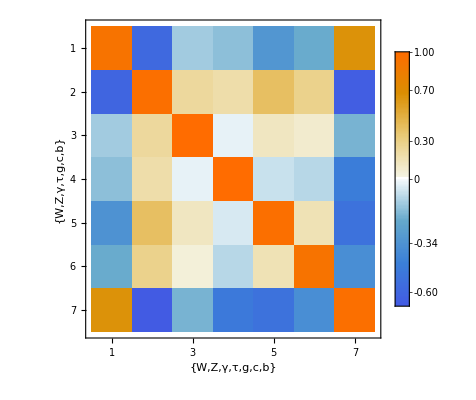

```mathematica
MatrixPlot[%40,FrameLabel->{{"W","Z","γ","τ","g","c","b"},{"W","Z","γ","τ","g","c","b"}},PlotLegends->Automatic]
```

```mathematica
Eigenvalues[%21]
```

{1.45764×10^6,221226.,67099.7,48535.6,30937.8,15919.6,987.163}

### 10p_MI_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2,kz^2 kb^2/ktotal,kz^2 kt^2/ktotal,kz^2 kg^2/ktotal,kz^2 kw^2/ktotal,kz^2 ktau^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kz^2 kmu^2/ktotal,kw^2 kb^2/ktotal,kz^2brinv+1};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100,0.14/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 10p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{10,2.5,1,0.5}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0420525
-0.0403854) | (0.0208194
-0.0204033) | (0.0131192
-0.0129528) | (0.00925944
-0.00917626)
(0.0549682
-0.0530561) | (0.0272377
-0.0267595) | (0.0171701
-0.0169788) | (0.012121
-0.0120254)
(0.0494335
-0.0474334) | (0.0244641
-0.0239643) | (0.015414
-0.0152141) | (0.0108786
-0.0107786)
(0.0387409
-0.0385975) | (0.0193637
-0.0193283) | (0.012244
-0.0122299) | (0.00865667
-0.00864962)
(0.0464184
-0.0444732) | (0.0229652
-0.0224792) | (0.0144679
-0.0142735) | (0.0102101
-0.010113)
(0.00803156
-0.00809659) | (0.00402379
-0.00404005) | (0.00254676
-0.00255326) | (0.0018015
-0.00180475)
(0.14182
-0.157784) | (0.0723428
-0.0762269) | (0.0461336
-0.0476789) | (0.0327644
-0.0335357)
(0.245948
-0.320985) | (0.128651
-0.145883) | (0.082924
-0.0897124) | (0.0592333
-0.0626106)
(0.00442776
-0.00442774) | (0.00221367
-0.00221367) | (0.00140002
-0.00140002) | (0.000989956
-0.000989956)
(0.0910399
-0.0834866) | (0.0445451
-0.0426581) | (0.0279496
-0.0271949) | (0.0196843
-0.019307))

## CDR

### SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

### Prep (input)

```mathematica
(*higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsprecepc={15.9,0.888,8.32,1.03,5.07,1.42,3.55,(0.00326191+0.00326551)*100/2,(0.0311003+0.0312155)*100/2,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;
inputcorrelations=(*Nov.6.2017*){{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
inputcorrelations=(*Jan.7.2018*){{100,-2.58,-0.29,-0.58,-0.16,0.40,-0.68,0.14,-0.06,0.09,0},{-2.58,100,-6.14,-18.57,-6.47,9.50,-5.36,3.45,-1.58,-0.51,0},{-0.29,-6.14,100,0.33,-0.38,0.08,-0.63,0.06,-0.03,0.14,0},{-0.58,-18.57,0.33,100,-16.34,-33.83,-13.56,-8.42,3.87,1.10,0},{-0.16,-6.47,-0.38,-16.34,100,-10.85,-6.65,-11.85,5.44,-4.15,0},{0.40,9.50,0.08,-33.83,-10.85,100,-16.72,-6.77,3.11,-1.05,0},{-0.68,-5.36,-0.63,-13.56,-6.65,-16.72,100,-4.13,1.90,-6.20,0},{0.14,3.45,0.06,-8.42,-11.85,-6.77,-4.13,100,-45.91,1.35,0},
{-0.06,-1.58,-0.03,3.87,5.44,3.11,1.90,-45.91,100,-0.62,0},{0.09,-0.51,0.14,1.10,-4.15,-1.05,-6.20,1.35,-0.62,100,0},{0,0,0,0,0,0,0,0,0,0,100}};
halfcorrelation=(*Apr.15.2018*)SparseArray[{{11,11}->0,{4,2}->-22.661,{5,2}->-14.181,{6,2}->9.214,{7,2}->2.329,{8,2}->4.237,{9,2}->-1.974,{10,2}->0.257,{5,4}->-12.487,{6,4}->-27.633,{7,4}->-10.609,{8,4}->-7.886,{9,4}->3.675,{10,4}->1.658,{6,5}->-13.483,{7,5}->-6.800,{8,5}->-12.420,{9,5}->5.788,{10,5}->-4.351,{7,6}->-19.209,{8,6}->-7.648,{9,6}-> 3.564,{10,6}->-1.081,{8,7}-> -4.463,{9,7}-> 2.080,{10,7}-> -6.389,{9,8}-> -46.606,{10,8}-> 1.335,{10,9}-> -0.622}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
(*chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[If[i==j,((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])/lumif,0],{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]*)*)
```

### Defining χ^2 s

```mathematica
(*Following Frederick James P.68-69 for defintions of correlation matrix, covariance matrix, etc.*)
(*inverseinputcorrelations is actually the precision/conentration matrix*)
```

```mathematica
Inverse[{{1,ρ},{ρ,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2)
-ρ/(1-ρ^2) | 1/(1-ρ^2))

```mathematica
Inverse[{{1,ρ,0},{ρ,1,0},{0,0,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2) | 0
-ρ/(1-ρ^2) | 1/(1-ρ^2) | 0
0 | 0 | 1)

```mathematica
inverseinputcorrelations=Inverse[inputcorrelations/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03208 | 0. | 0.178022 | 0.126431 | 0.0000829784 | 0.0000541663 | 0.000663357 | 0.000292187 | 3.08409×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.178022 | 0. | 1.15222 | 0.386438 | 0.059681 | 0.0500988 | 0.00486027 | 0.0000485866 | -4.04817×10^-6 | 0.
0. | 0.126431 | 0. | 0.386438 | 1.13518 | 0.0457993 | 0.0354664 | 0.0243613 | 0.0000328205 | -2.22321×10^-6 | 0.
0. | 0.0000829784 | 0. | 0.059681 | 0.0457993 | 1.07973 | 0.256208 | 0.152045 | -3.46304×10^-6 | 0.0331285 | 0.
0. | 0.0000541663 | 0. | 0.0500988 | 0.0354664 | 0.256208 | 1.07128 | 0.106524 | -3.60363×10^-6 | 0.0727213 | 0.
0. | 0.000663357 | 0. | 0.00486027 | 0.0243613 | 0.152045 | 0.106524 | 1.29084 | 0.577755 | 1.4814×10^-6 | 0.
0. | 0.000292187 | 0. | 0.0000485866 | 0.0000328205 | -3.46304×10^-6 | -3.60363×10^-6 | 0.577755 | 1.26407 | 5.01996×10^-6 | 0.
0. | 3.08409×10^-6 | 0. | -4.04817×10^-6 | -2.22321×10^-6 | 0.0331285 | 0.0727213 | 1.4814×10^-6 | 5.01996×10^-6 | 1.00528 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inverseinputcorrelationslhc7s2=Inverse[inputcorrelationslhc7s2/100];
```

```mathematica
Length[higgsprecepc]
Length[higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau]]
Dimensions[inverseinputcorrelations]
```

11

11

{11,11}

```mathematica
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
(*higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/lumif,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}](*Sum[(higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgsprelhc7s2[[i]]^2,{i,1,Length[higgsprelhc7s2]}]*)
```

```mathematica
Length[higgsprecepc]
```

11

```mathematica
Length[higgsprelhc7s2]
```

8

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
(*higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};*)
chisquarecepc10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[((higgsobslhc7s2[kz/Sqrt[ktotal],kw/Sqrt[ktotal],kg/Sqrt[ktotal],kgamma/Sqrt[ktotal],kb/Sqrt[ktotal],kt/Sqrt[ktotal],ktau/Sqrt[ktotal],kmu/Sqrt[ktotal]][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz/Sqrt[ktotal],kw/Sqrt[ktotal],kg/Sqrt[ktotal],kgamma/Sqrt[ktotal],kb/Sqrt[ktotal],kt/Sqrt[ktotal],ktau/Sqrt[ktotal],kmu/Sqrt[ktotal]][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/lumif+(kz^2 brinv)^2/0.0235^2,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]
```

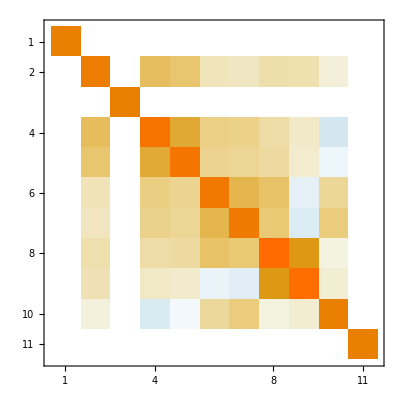

```mathematica
MatrixPlot[inverseinputcorrelations]
```

```mathematica
inverseinputcorrelations//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03208 | 0. | 0.178022 | 0.126431 | 0.0000829784 | 0.0000541663 | 0.000663357 | 0.000292187 | 3.08409×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.178022 | 0. | 1.15222 | 0.386438 | 0.059681 | 0.0500988 | 0.00486027 | 0.0000485866 | -4.04817×10^-6 | 0.
0. | 0.126431 | 0. | 0.386438 | 1.13518 | 0.0457993 | 0.0354664 | 0.0243613 | 0.0000328205 | -2.22321×10^-6 | 0.
0. | 0.0000829784 | 0. | 0.059681 | 0.0457993 | 1.07973 | 0.256208 | 0.152045 | -3.46304×10^-6 | 0.0331285 | 0.
0. | 0.0000541663 | 0. | 0.0500988 | 0.0354664 | 0.256208 | 1.07128 | 0.106524 | -3.60363×10^-6 | 0.0727213 | 0.
0. | 0.000663357 | 0. | 0.00486027 | 0.0243613 | 0.152045 | 0.106524 | 1.29084 | 0.577755 | 1.4814×10^-6 | 0.
0. | 0.000292187 | 0. | 0.0000485866 | 0.0000328205 | -3.46304×10^-6 | -3.60363×10^-6 | 0.577755 | 1.26407 | 5.01996×10^-6 | 0.
0. | 3.08409×10^-6 | 0. | -4.04817×10^-6 | -2.22321×10^-6 | 0.0331285 | 0.0727213 | 1.4814×10^-6 | 5.01996×10^-6 | 1.00528 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inputcorrelations-inputcorrelationsᵀ//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0123056
-0.0122817)
(0.0221704
-0.0221089)
(0.0151907
-0.0150724)
(0.0137625
-0.0137624)
(0.0138986
-0.0138134)
(0.00126325
-0.00126505)
(0.0381626
-0.0390288))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100},3]ᵀ//MatrixForm
```

(kb | {{1.23,-1.23}}
kc | {{2.22,-2.21}}
kg | {{1.52,-1.51}}
kw | {{1.38,-1.38}}
ktau | {{1.39,-1.38}}
kz | {{0.13,-0.13}}
kgamma | {{3.82,-3.9}})

```mathematica
concentrationmatrix7p=Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2;
%//MatrixForm
```

(142323. | -5645.58 | -21599.9 | -50634. | -45274.6 | 111489. | -738.934
-5645.58 | 3621.96 | 1917.9 | 306.152 | -1102.38 | -8714.28 | 1.71332
-21599.9 | 1917.9 | 22268. | -1096.87 | -4109.46 | -18857.1 | -15.7192
-50634. | 306.152 | -1096.87 | 47991.3 | -974.15 | -68821.1 | 4.00072
-45274.6 | -1102.38 | -4109.46 | -974.15 | 49537.9 | 18439. | -86.4234
111489. | -8714.28 | -18857.1 | -68821.1 | 18439. | 832263. | -880.244
-738.934 | 1.71332 | -15.7192 | 4.00072 | -86.4234 | -880.244 | 761.443)

```mathematica
covariancematrix7p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7].concentrationmatrix7p.(((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7])];
%//MatrixForm
```

(1.00022 | 0.630463 | 0.888118 | 0.935191 | 0.944835 | -0.323107 | 0.340064
0.630463 | 0.999868 | 0.492795 | 0.594193 | 0.607826 | -0.109998 | 0.217068
0.888118 | 0.492795 | 1.00013 | 0.843744 | 0.854183 | -0.23333 | 0.306372
0.935191 | 0.594193 | 0.843744 | 1.00022 | 0.883256 | -0.184152 | 0.32228
0.944835 | 0.607826 | 0.854183 | 0.883256 | 1.00016 | -0.324982 | 0.324978
-0.323107 | -0.109998 | -0.23333 | -0.184152 | -0.324982 | 1. | -0.0766545
0.340064 | 0.217068 | 0.306372 | 0.32228 | 0.324978 | -0.0766545 | 0.99868)

```mathematica
correlationmatrix7p=Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]].covariancematrix7p.Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.630434 | 0.887962 | 0.934984 | 0.944652 | -0.323071 | 0.340251
0.630434 | 1. | 0.492796 | 0.594166 | 0.607817 | -0.110005 | 0.217226
0.887962 | 0.492796 | 1. | 0.843597 | 0.854059 | -0.233315 | 0.306555
0.934984 | 0.594166 | 0.843597 | 1. | 0.883087 | -0.184132 | 0.322458
0.944652 | 0.607817 | 0.854059 | 0.883087 | 1. | -0.324955 | 0.325167
-0.323071 | -0.110005 | -0.233315 | -0.184132 | -0.324955 | 1. | -0.0767052
0.340251 | 0.217226 | 0.306555 | 0.322458 | 0.325167 | -0.0767052 | 1.)

### 7p_fit_CEPC_LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100,cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.23,-1.23}} | {{0.75,-0.75}}
kc | {{2.22,-2.21}} | {{1.74,-1.74}}
kg | {{1.52,-1.51}} | {{0.92,-0.91}}
kw | {{1.38,-1.38}} | {{0.85,-0.85}}
ktau | {{1.39,-1.38}} | {{0.86,-0.85}}
kz | {{0.13,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.82,-3.9}} | {{1.76,-1.76}})

```mathematica
CDRresult=SetAccuracy[({{kb, {{1.1802939176687561318`3.0719901691086693,-1.1779947340898035968`3.0711433490581697}}, {{0.9197434346150625828`2.9636666963991947,-0.9172886628042468127`2.962506025893967}}}, {kc, {{2.1133926907131730388`3.32498020105821,-2.1074309458573661225`3.3237533530123526}}, {{1.8618403746730294301`3.269942443900768,-1.8613309632845922437`3.2698236019048914}}}, {kg, {{1.4580201978151960951`3.1637635402638,-1.4470375661800065625`3.160479805875713}}, {{1.1197659218210345156`3.049127246343211,-1.1129849147994486103`3.0464892780240564}}}, {kw, {{1.3065999737734512731`3.1161426451364775,-1.3066112939106404589`3.1161464077661405}}, {{1.0192136691447377661`3.008265239553995,-1.0184521615326214139`3.007940634248957}}}, {ktau, {{1.3353651352430182531`3.1256000331456053,-1.327386804726191194`3.1229974960971303}}, {{1.062794739058968263`3.0264493959421217,-1.0567580318092411051`3.0239755573358593}}}, {kz, {{0.1249436401823528497`2.096714154788162,-0.125110532339467978`2.0972938719985508}}, {{0.1210227905475330101`2.0828671626884825,-0.1211510064978167656`2.0833270265183628}}}, {kgamma, {{3.6111055639962503783`3.5576401844088106,-3.6868600986080872772`3.5666566582040904}}, {{1.6058221714330700447`3.2056974498832576,-1.6096675187487814451`3.2067361805757737}}}}),3]//MatrixForm
```

(kb | {{1.18,-1.18}} | {{0.92,-0.92}}
kc | {{2.11,-2.11}} | {{1.86,-1.86}}
kg | {{1.46,-1.45}} | {{1.12,-1.11}}
kw | {{1.31,-1.31}} | {{1.02,-1.02}}
ktau | {{1.34,-1.33}} | {{1.06,-1.06}}
kz | {{0.12,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.61,-3.69}} | {{1.61,-1.61}})

```mathematica
concentrationmatrix7pL=Table[D[chisquarecepcL[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2
```

{{143305.,-5904.49,-21815.2,-50571.7,-45328.,111692.,-940.681},{-5904.49,6631.77,1272.06,-1769.46,-2338.67,-9525.28,-1811.68},{-21815.2,1272.06,28341.3,-2424.38,-4553.24,-20023.7,574.162},{-50571.7,-1769.46,-2424.38,56238.8,-1139.98,-70475.3,523.093},{-45328.,-2338.67,-4553.24,-1139.98,55594.,16403.5,-167.802},{111692.,-9525.28,-20023.7,-70475.3,16403.5,838396.,-190.145},{-940.681,-1811.68,574.162,523.093,-167.802,-190.145,4041.74}}

```mathematica
covariancematrix7pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7].concentrationmatrix7pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7])];
%//MatrixForm
```

(1.00002 | 0.628395 | 0.745599 | 0.845851 | 0.863714 | -0.20968 | 0.285769
0.628395 | 0.999936 | 0.42865 | 0.585426 | 0.58882 | -0.0142298 | 0.447609
0.745599 | 0.42865 | 1.00001 | 0.666444 | 0.676093 | -0.0664381 | 0.161473
0.845851 | 0.585426 | 0.666444 | 1.00003 | 0.736507 | 0.00448111 | 0.245859
0.863714 | 0.58882 | 0.676093 | 0.736507 | 1.00002 | -0.199274 | 0.26948
-0.20968 | -0.0142298 | -0.0664381 | 0.00448111 | -0.199274 | 0.999999 | -0.0232448
0.285769 | 0.447609 | 0.161473 | 0.245859 | 0.26948 | -0.0232448 | 0.999974)

```mathematica
correlationmatrix7pL=Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]].covariancematrix7pL.Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.628407 | 0.745586 | 0.845829 | 0.863697 | -0.209678 | 0.285769
0.628407 | 1. | 0.428661 | 0.585437 | 0.588834 | -0.0142303 | 0.447629
0.745586 | 0.428661 | 1. | 0.66643 | 0.676084 | -0.0664377 | 0.161474
0.845829 | 0.585437 | 0.66643 | 1. | 0.736491 | 0.00448105 | 0.245859
0.863697 | 0.588834 | 0.676084 | 0.736491 | 1. | -0.199272 | 0.269481
-0.209678 | -0.0142303 | -0.0664377 | 0.00448105 | -0.199272 | 1. | -0.0232451
0.285769 | 0.447629 | 0.161474 | 0.245859 | 0.269481 | -0.0232451 | 1.)

### 10p-fit-CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0129954
-0.0129245)
(0.0216494
-0.0215376)
(0.0155011
-0.0153488)
(0.0138088
-0.0137778)
(0.0145525
-0.0144235)
(0.00249676
-0.00250313)
(0.0364716
-0.0371533)
(0.0834764
-0.0901677)
(0.00150002
-0.0015)
(0.0287935
-0.0281478))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}}
kt | {{2.16,-2.15}}
kg | {{1.55,-1.53}}
kw | {{1.38,-1.38}}
ktau | {{1.46,-1.44}}
kz | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}}
kmu | {{8.35,-9.02}}
brinv | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}})

```mathematica
concentrationmatrix10p=Table[D[chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10].concentrationmatrix10p.(((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10])];
%//MatrixForm
```

(1.00017 | 0.651846 | 0.903239 | 0.933433 | 0.95559 | 0.192906 | 0.366548 | 0.155416 | 0. | 0.981766
0.651846 | 0.999877 | 0.525309 | 0.614638 | 0.63255 | 0.115778 | 0.242468 | 0.102806 | 0. | 0.647351
0.903239 | 0.525309 | 1.0001 | 0.857996 | 0.875629 | 0.162078 | 0.335991 | 0.14246 | 0. | 0.897332
0.933433 | 0.614638 | 0.857996 | 1.0002 | 0.89039 | 0.181251 | 0.347828 | 0.147479 | 0. | 0.93131
0.95559 | 0.63255 | 0.875629 | 0.89039 | 1.00012 | 0.17256 | 0.353482 | 0.149876 | 0. | 0.944405
0.192906 | 0.115778 | 0.162078 | 0.181251 | 0.17256 | 1.00004 | 0.0679133 | 0.0287951 | 0. | 0.351246
0.366548 | 0.242468 | 0.335991 | 0.347828 | 0.353482 | 0.0679133 | 0.998814 | 0.0575404 | 0. | 0.362869
0.155416 | 0.102806 | 0.14246 | 0.147479 | 0.149876 | 0.0287951 | 0.0575404 | 0.994175 | 0. | 0.153856
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999989 | 0.
0.981766 | 0.647351 | 0.897332 | 0.93131 | 0.944405 | 0.351246 | 0.362869 | 0.153856 | 0. | 1.00006)

```mathematica
correlationmatrix10p=Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]].covariancematrix10p.Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.651831 | 0.903117 | 0.933261 | 0.955451 | 0.192886 | 0.366734 | 0.155857 | 0. | 0.981654
0.651831 | 1. | 0.525314 | 0.614615 | 0.63255 | 0.115783 | 0.242627 | 0.103113 | 0. | 0.647372
0.903117 | 0.525314 | 1. | 0.857867 | 0.875532 | 0.162067 | 0.336173 | 0.142869 | 0. | 0.897261
0.933261 | 0.614615 | 0.857867 | 1. | 0.890247 | 0.181229 | 0.348 | 0.147895 | 0. | 0.93119
0.955451 | 0.63255 | 0.875532 | 0.890247 | 1. | 0.172546 | 0.353671 | 0.150305 | 0. | 0.94432
0.192886 | 0.115783 | 0.162067 | 0.181229 | 0.172546 | 1. | 0.0679522 | 0.0288788 | 0. | 0.351228
0.366734 | 0.242627 | 0.336173 | 0.348 | 0.353671 | 0.0679522 | 1. | 0.057743 | 0. | 0.363073
0.155857 | 0.103113 | 0.142869 | 0.147895 | 0.150305 | 0.0288788 | 0.057743 | 1. | 0. | 0.154301
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.981654 | 0.647372 | 0.897261 | 0.93119 | 0.94432 | 0.351228 | 0.363073 | 0.154301 | 0. | 1.)

### 10p-fit-CEPC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL//MatrixForm
```

((0.00927207
-0.00916595)
(0.0173303
-0.0172729)
(0.0118692
-0.0117277)
(0.010024
-0.0099338)
(0.0105663
-0.010432)
(0.00243839
-0.00244359)
(0.0145488
-0.0144177)
(0.0422674
-0.0423455)
(0.00133591
-0.00133591)
(0.0209205
-0.0204368))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}} | {{0.93,-0.92}}
kt | {{2.16,-2.15}} | {{1.73,-1.73}}
kg | {{1.55,-1.53}} | {{1.19,-1.17}}
kw | {{1.38,-1.38}} | {{1.,-0.99}}
ktau | {{1.46,-1.44}} | {{1.06,-1.04}}
kz | {{0.25,-0.25}} | {{0.24,-0.24}}
kgamma | {{3.65,-3.72}} | {{1.45,-1.44}}
kmu | {{8.35,-9.02}} | {{4.23,-4.23}}
brinv | {{0.15,-0.15}} | {{0.13,-0.13}}
ktotal | {{2.88,-2.81}} | {{2.09,-2.04}})

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}} | {{0.93,-0.92}}
kt | {{2.16,-2.15}} | {{1.73,-1.73}}
kg | {{1.55,-1.53}} | {{1.19,-1.17}}
kw | {{1.38,-1.38}} | {{1.,-0.99}}
ktau | {{1.46,-1.44}} | {{1.06,-1.04}}
kz | {{0.25,-0.25}} | {{0.24,-0.24}}
kgamma | {{3.65,-3.72}} | {{1.45,-1.44}}
kmu | {{8.35,-9.02}} | {{4.23,-4.23}}
brinv | {{0.15,-0.15}} | {{0.13,-0.13}}
ktotal | {{2.88,-2.81}} | {{2.09,-2.04}})

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL},2]ᵀ//MatrixForm
```

(kb | 1.3 | 0.9
kt | 2.2 | 1.7
kg | 1.5 | 1.2
kw | 1.4 | 1.
ktau | 1.4 | 1.
kz | 0.2 | 0.2
kgamma | 3.7 | 1.4
kmu | 8.7 | 4.2
brinv | 0.2 | 0.1
ktotal | 2.8 | 2.1)

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249995,0.0368124,0.086822,0.00150001,0.0284707}

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249995,0.0368124,0.086822,0.00150001,0.0284707}

```mathematica
concentrationmatrix10pL=Table[D[chisquarecepc10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10].concentrationmatrix10pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10])];
%//MatrixForm
```

(1.00002 | 0.544249 | 0.851549 | 0.888481 | 0.92072 | 0.195561 | 0.544303 | 0.19371 | 0. | 0.965489
0.544249 | 0.999833 | 0.401598 | 0.492802 | 0.515419 | 0.111182 | 0.284932 | 0.112517 | 0. | 0.540706
0.851549 | 0.401598 | 0.999962 | 0.776499 | 0.804719 | 0.167392 | 0.455482 | 0.156521 | 0. | 0.843562
0.888481 | 0.492802 | 0.776499 | 1.00004 | 0.819314 | 0.199914 | 0.524021 | 0.185936 | 0. | 0.888795
0.92072 | 0.515419 | 0.804719 | 0.819314 | 0.999978 | 0.17638 | 0.533463 | 0.186003 | 0. | 0.903497
0.195561 | 0.111182 | 0.167392 | 0.199914 | 0.17638 | 0.999996 | 0.167757 | 0.0584316 | 0. | 0.409957
0.544303 | 0.284932 | 0.455482 | 0.524021 | 0.533463 | 0.167757 | 0.999935 | 0.14833 | 0. | 0.548518
0.19371 | 0.112517 | 0.156521 | 0.185936 | 0.186003 | 0.0584316 | 0.14833 | 1.00323 | 0. | 0.194797
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999997 | 0.
0.965489 | 0.540706 | 0.843562 | 0.888795 | 0.903497 | 0.409957 | 0.548518 | 0.194797 | 0. | 0.999847)

```mathematica
Sqrt[Diagonal[covariancematrix10pL]]
```

{1.00001,0.999917,0.999981,1.00002,0.999989,0.999998,0.999968,1.00161,0.999998,0.999924}

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.54429 | 0.851558 | 0.888457 | 0.920723 | 0.19556 | 0.544316 | 0.193397 | 0. | 0.965555
0.54429 | 1. | 0.401639 | 0.492833 | 0.515467 | 0.111191 | 0.284965 | 0.112345 | 0. | 0.540792
0.851558 | 0.401639 | 1. | 0.776499 | 0.804743 | 0.167396 | 0.455506 | 0.156271 | 0. | 0.843642
0.888457 | 0.492833 | 0.776499 | 1. | 0.819306 | 0.19991 | 0.524027 | 0.185633 | 0. | 0.888845
0.920723 | 0.515467 | 0.804743 | 0.819306 | 1. | 0.176382 | 0.533486 | 0.185705 | 0. | 0.903576
0.19556 | 0.111191 | 0.167396 | 0.19991 | 0.176382 | 1. | 0.167763 | 0.0583376 | 0. | 0.409989
0.544316 | 0.284965 | 0.455506 | 0.524027 | 0.533486 | 0.167763 | 1. | 0.148096 | 0. | 0.548577
0.193397 | 0.112345 | 0.156271 | 0.185633 | 0.185705 | 0.0583376 | 0.148096 | 1. | 0. | 0.194498
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.965555 | 0.540792 | 0.843642 | 0.888845 | 0.903576 | 0.409989 | 0.548577 | 0.194498 | 0. | 1.)

```mathematica
correlationmatrix10pL//MatrixForm
```

(1. | 0.54429 | 0.851558 | 0.888457 | 0.920723 | 0.19556 | 0.544316 | 0.193397 | 0. | 0.965555
0.54429 | 1. | 0.401639 | 0.492833 | 0.515467 | 0.111191 | 0.284965 | 0.112345 | 0. | 0.540792
0.851558 | 0.401639 | 1. | 0.776499 | 0.804743 | 0.167396 | 0.455506 | 0.156271 | 0. | 0.843642
0.888457 | 0.492833 | 0.776499 | 1. | 0.819306 | 0.19991 | 0.524027 | 0.185633 | 0. | 0.888845
0.920723 | 0.515467 | 0.804743 | 0.819306 | 1. | 0.176382 | 0.533486 | 0.185705 | 0. | 0.903576
0.19556 | 0.111191 | 0.167396 | 0.19991 | 0.176382 | 1. | 0.167763 | 0.0583376 | 0. | 0.409989
0.544316 | 0.284965 | 0.455506 | 0.524027 | 0.533486 | 0.167763 | 1. | 0.148096 | 0. | 0.548577
0.193397 | 0.112345 | 0.156271 | 0.185633 | 0.185705 | 0.0583376 | 0.148096 | 1. | 0. | 0.194498
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.965555 | 0.540792 | 0.843642 | 0.888845 | 0.903576 | 0.409989 | 0.548577 | 0.194498 | 0. | 1.)

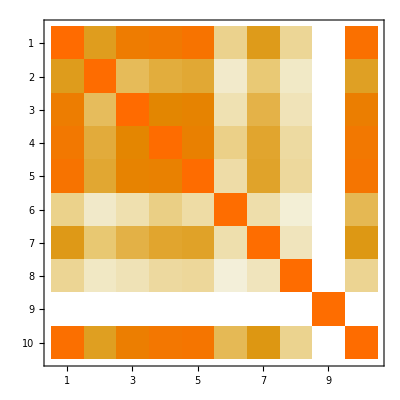

```mathematica
MatrixPlot[correlationmatrix10pL]
```

## CDR (width subchannel ZZ)

```mathematica
(*It is triky now to define subchannel fit; there are two approaches, which might cause confusion, I list them here*)
(*1: freeze all the other measurements/parameters, techinically means we set the precision to infinity for iirelevant channels; this will first improve a given cross section measurement, then we combine. In other words, the fit input precision will change for the relevant channels. It then will be hard to combine different channels as they will correspond to different degree of freedoms.*)
(*2: use the same input precision but remove the correlation entries with irrelavant ones, then calculate. This avoids the problem above. I will take the second approach.*)
```

```mathematica
higgsprecepcoriginal=higgsprecepc
```

{0.171,0.0082,0.0684,0.0098,0.0509,0.0127,0.0326,0.003068,0.029991,∞,0.005}

```mathematica
higgsprecepc=Table[If[i==5||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,∞,0.0509,∞,∞,∞,∞,∞,0.005}

```mathematica
inputcorrelationsoriginal=inputcorrelations;
```

```mathematica
inverseinputcorrelations=Inverse[(IdentityMatrix[11]*100+SparseArray[{{11,11}->0,{5,11}->inputcorrelationsoriginal[[5,11]]}]+SparseArray[{{11,11}->0,{5,11}->inputcorrelationsoriginal[[5,11]]}]ᵀ)/100]
```

{{1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={Infinity,Infinity,Infinity,Infinity,5.07,Infinity,Infinity,Infinity,Infinity,Infinity,0.5}/100;
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+40000. (-1+kz^2)^2+389.031 (-1+kz^4/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[%,kz][[1]]},{x,-0.2,0.2,0.002}]
```

{{-0.2,22.9286},{-0.198,22.3667},{-0.196,21.8142},{-0.194,21.2712},{-0.192,20.7376},{-0.19,20.2131},{-0.188,19.6978},{-0.186,19.1914},{-0.184,18.6939},{-0.182,18.2052},{-0.18,17.7252},{-0.178,17.2537},{-0.176,16.7907},{-0.174,16.3361},{-0.172,15.8898},{-0.17,15.4516},{-0.168,15.0215},{-0.166,14.5993},{-0.164,14.1851},{-0.162,13.7786},{-0.16,13.3799},{-0.158,12.9887},{-0.156,12.6051},{-0.154,12.2289},{-0.152,11.86},{-0.15,11.4984},{-0.148,11.1439},{-0.146,10.7966},{-0.144,10.4562},{-0.142,10.1228},{-0.14,9.79615},{-0.138,9.4763},{-0.136,9.16313},{-0.134,8.85655},{-0.132,8.5565},{-0.13,8.2629},{-0.128,7.97566},{-0.126,7.69473},{-0.124,7.42001},{-0.122,7.15145},{-0.12,6.88896},{-0.118,6.63248},{-0.116,6.38194},{-0.114,6.13726},{-0.112,5.89839},{-0.11,5.66525},{-0.108,5.43777},{-0.106,5.2159},{-0.104,4.99956},{-0.102,4.78869},{-0.1,4.58323},{-0.098,4.38311},{-0.096,4.18828},{-0.094,3.99866},{-0.092,3.81421},{-0.09,3.63486},{-0.088,3.46055},{-0.086,3.29123},{-0.084,3.12683},{-0.082,2.9673},{-0.08,2.81258},{-0.078,2.66263},{-0.076,2.51737},{-0.074,2.37676},{-0.072,2.24075},{-0.07,2.10928},{-0.068,1.9823},{-0.066,1.85976},{-0.064,1.7416},{-0.062,1.62778},{-0.06,1.51825},{-0.058,1.41295},{-0.056,1.31184},{-0.054,1.21487},{-0.052,1.12199},{-0.05,1.03316},{-0.048,0.948325},{-0.046,0.867444},{-0.044,0.790471},{-0.042,0.71736},{-0.04,0.648066},{-0.038,0.582547},{-0.036,0.520759},{-0.034,0.462659},{-0.032,0.408204},{-0.03,0.357354},{-0.028,0.310065},{-0.026,0.266298},{-0.024,0.226012},{-0.022,0.189167},{-0.02,0.155723},{-0.018,0.125642},{-0.016,0.0988852},{-0.014,0.0754138},{-0.012,0.0551905},{-0.01,0.0381779},{-0.008,0.0243391},{-0.006,0.0136378},{-0.004,0.00603783},{-0.002,0.00150364},{0.,0.},{0.002,0.0014921},{0.004,0.00594552},{0.006,0.0133262},{0.008,0.0236006},{0.01,0.0367353},{0.012,0.0526976},{0.014,0.0714548},{0.016,0.0929748},{0.018,0.117226},{0.02,0.144177},{0.022,0.173796},{0.024,0.206053},{0.026,0.240918},{0.028,0.278359},{0.03,0.318349},{0.032,0.360857},{0.034,0.405854},{0.036,0.453312},{0.038,0.503202},{0.04,0.555495},{0.042,0.610166},{0.044,0.667185},{0.046,0.726525},{0.048,0.788161},{0.05,0.852064},{0.052,0.91821},{0.054,0.986572},{0.056,1.05712},{0.058,1.12984},{0.06,1.2047},{0.062,1.28167},{0.064,1.36073},{0.066,1.44186},{0.068,1.52503},{0.07,1.61022},{0.072,1.6974},{0.074,1.78655},{0.076,1.87766},{0.078,1.97068},{0.08,2.06562},{0.082,2.16243},{0.084,2.2611},{0.086,2.36161},{0.088,2.46393},{0.09,2.56805},{0.092,2.67394},{0.094,2.78159},{0.096,2.89096},{0.098,3.00205},{0.1,3.11483},{0.102,3.22928},{0.104,3.34538},{0.106,3.46311},{0.108,3.58246},{0.11,3.7034},{0.112,3.82591},{0.114,3.94998},{0.116,4.07559},{0.118,4.20272},{0.12,4.33134},{0.122,4.46145},{0.124,4.59303},{0.126,4.72605},{0.128,4.86051},{0.13,4.99638},{0.132,5.13364},{0.134,5.27228},{0.136,5.41229},{0.138,5.55364},{0.14,5.69633},{0.142,5.84033},{0.144,5.98562},{0.146,6.1322},{0.148,6.28005},{0.15,6.42914},{0.152,6.57948},{0.154,6.73103},{0.156,6.88379},{0.158,7.03775},{0.16,7.19288},{0.162,7.34917},{0.164,7.50661},{0.166,7.66518},{0.168,7.82488},{0.17,7.98568},{0.172,8.14757},{0.174,8.31054},{0.176,8.47458},{0.178,8.63967},{0.18,8.80579},{0.182,8.97295},{0.184,9.14111},{0.186,9.31028},{0.188,9.48044},{0.19,9.65157},{0.192,9.82366},{0.194,9.9967},{0.196,10.1707},{0.198,10.3456},{0.2,10.5214}}

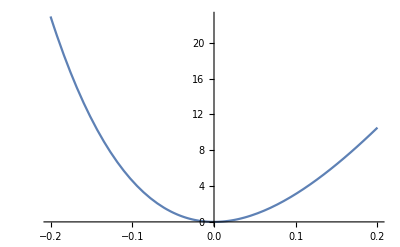

{{x→0.0543855}}

```mathematica
Plot[Interpolation[tempdata][x],{x,-0.2,0.2}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

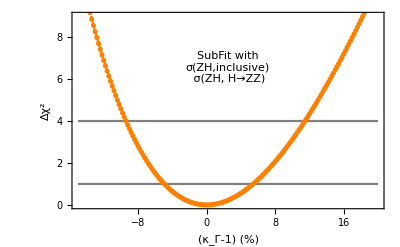

{{x→0.0543855}}

```mathematica
Show[Plot[{Interpolation[tempdata][x/100],1,4},{x,-0.15*100,0.2*100},PlotRange->{0,9},Frame->True,FrameLabel->{"(κ_Γ-1) (%)","Δχ^2"},BaseStyle->16,PlotStyle->{Orange,Gray,Gray}],ListPlot[{#[[1]]*100,#[[2]]}&/@tempdata,PlotStyle->Orange],Epilog->Inset[Framed[Style["SubFit with\nσ(ZH,inclusive)\n σ(ZH, H→ZZ)",13],FrameStyle->None,Background->White],Scaled[{0.5,0.72}]]]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

## CDR (width subchannel WW)

```mathematica
higgsprecepc=Table[If[i==4||i==8||i==9||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,0.0098,∞,∞,∞,0.003068,0.029991,∞,0.005}

```mathematica
inverseinputcorrelations=Inverse[(IdentityMatrix[11]*100+SparseArray[{{11,11}->0,{4,8}->inputcorrelationsoriginal[[4,8]],{4,9}->inputcorrelationsoriginal[[4,9]],{4,11}->inputcorrelationsoriginal[[4,11]],{8,9}->inputcorrelationsoriginal[[8,9]],{8,11}->inputcorrelationsoriginal[[8,11]],{9,11}->inputcorrelationsoriginal[[9,11]]}]+SparseArray[{{11,11}->0,{4,8}->inputcorrelationsoriginal[[4,8]],{4,9}->inputcorrelationsoriginal[[4,9]],{4,11}->inputcorrelationsoriginal[[4,11]],{8,9}->inputcorrelationsoriginal[[8,9]],{8,11}->inputcorrelationsoriginal[[8,11]],{9,11}->inputcorrelationsoriginal[[9,11]]}]ᵀ)/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.00009 | 0. | 0. | 0. | -0.00969845 | 5.10855×10^-6 | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.00969845 | 0. | 0. | 0. | 1.30284 | 0.628015 | 0. | 0.
0. | 0. | 0. | 5.10855×10^-6 | 0. | 0. | 0. | 0.628015 | 1.30275 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+1448.37 (-1+(kb^2 kw^2)/ktotal)^2+40000. (-1+kz^2)^2+13650.7 (-1+(kb^2 kw^2)/ktotal) (-1+(kb^2 kz^2)/ktotal)+138414. (-1+(kb^2 kz^2)/ktotal)^2+0.0347625 (-1+(kb^2 kw^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)-645.135 (-1+(kb^2 kz^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+10413.3 (-1+(kw^2 kz^2)/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[{%,0<kz<2,0<kw<2,0<kb<2},{kz,kw,kb}][[1]]},{x,-0.1,0.1,0.002}]
```

{{-0.1,8.67745},{-0.098,8.32755},{-0.096,7.9851},{-0.094,7.65009},{-0.092,7.3225},{-0.09,7.00231},{-0.088,6.6895},{-0.086,6.38407},{-0.084,6.086},{-0.082,5.79526},{-0.08,5.51185},{-0.078,5.23574},{-0.076,4.96693},{-0.074,4.70539},{-0.072,4.45112},{-0.07,4.20409},{-0.068,3.96428},{-0.066,3.7317},{-0.064,3.5063},{-0.062,3.28809},{-0.06,3.07705},{-0.058,2.87315},{-0.056,2.67639},{-0.054,2.48675},{-0.052,2.3042},{-0.05,2.12875},{-0.048,1.96037},{-0.046,1.79904},{-0.044,1.64475},{-0.042,1.49749},{-0.04,1.35724},{-0.038,1.22398},{-0.036,1.09769},{-0.034,0.978371},{-0.032,0.865995},{-0.03,0.76055},{-0.028,0.662019},{-0.026,0.570388},{-0.024,0.485642},{-0.022,0.407763},{-0.02,0.336738},{-0.018,0.27255},{-0.016,0.215184},{-0.014,0.164625},{-0.012,0.120857},{-0.01,0.0838643},{-0.008,0.0536322},{-0.006,0.0301451},{-0.004,0.0133876},{-0.002,0.00334435},{0.,1.00593×10^-21},{0.002,0.00333925},{0.004,0.0133468},{0.006,0.0300074},{0.008,0.0533057},{0.01,0.0832266},{0.012,0.119755},{0.014,0.162875},{0.016,0.212572},{0.018,0.268831},{0.02,0.331637},{0.022,0.400973},{0.024,0.476827},{0.026,0.559181},{0.028,0.648022},{0.03,0.743334},{0.032,0.845101},{0.034,0.95331},{0.036,1.06795},{0.038,1.18899},{0.04,1.31643},{0.042,1.45026},{0.044,1.59045},{0.046,1.73699},{0.048,1.88986},{0.05,2.04906},{0.052,2.21457},{0.054,2.38637},{0.056,2.56444},{0.058,2.74878},{0.06,2.93936},{0.062,3.13618},{0.064,3.33922},{0.066,3.54846},{0.068,3.76388},{0.07,3.98549},{0.072,4.21325},{0.074,4.44715},{0.076,4.68719},{0.078,4.93334},{0.08,5.1856},{0.082,5.44394},{0.084,5.70835},{0.086,5.97882},{0.088,6.25533},{0.09,6.53788},{0.092,6.82643},{0.094,7.12099},{0.096,7.42153},{0.098,7.72805},{0.1,8.04052}}

```mathematica
tempdata={{-0.1,8.677450891966563},{-0.098,8.32755196261379},{-0.096,7.985104085000047},{-0.094,7.65009132190818},{-0.092,7.322497744092595},{-0.09000000000000001,7.00230743052874},{-0.08800000000000001,6.689504468660578},{-0.08600000000000001,6.384072954645076},{-0.084,6.085996993594568},{-0.082,5.795260699816512},{-0.08,5.5118481970510524},{-0.07800000000000001,5.2357436187057855},{-0.07600000000000001,4.966931108088384},{-0.07400000000000001,4.705394818636952},{-0.07200000000000001,4.451118914147368},{-0.07,4.204087568999234},{-0.068,3.9642849683785095},{-0.066,3.731695308498466},{-0.064,3.5063027968179235},{-0.062000000000000006,3.288091652257446},{-0.060000000000000005,3.0770461054129132},{-0.058,2.8731503987672258},{-0.05600000000000001,2.6763887868992593},{-0.054000000000000006,2.4867455366909117},{-0.052000000000000005,2.3042049275318166},{-0.05,2.128751251521669},{-0.048,1.9603688136703976},{-0.046000000000000006,1.7990419320963464},{-0.044000000000000004,1.6447549382218103},{-0.042,1.497492176966834},{-0.04000000000000001,1.3572380069406136},{-0.038000000000000006,1.2239768006306484},{-0.036000000000000004,1.0976929445899921},{-0.034,0.9783708396221834},{-0.032,0.8659949009641101},{-0.03,0.7605495584667874},{-0.027999999999999997,0.662019256774069},{-0.02600000000000001,0.5703884554991236},{-0.024000000000000007,0.4856416293990754},{-0.022000000000000006,0.40776326854740963},{-0.020000000000000004,0.33673787850437903},{-0.018000000000000002,0.2725499804854658},{-0.016,0.2151841115277067},{-0.013999999999999999,0.1646248246541206},{-0.01200000000000001,0.12085668903607161},{-0.010000000000000009,0.08386429015371458},{-0.008000000000000007,0.05363222995443828},{-0.006000000000000005,0.03014512700938449},{-0.0040000000000000036,0.013387616668033502},{-0.0020000000000000018,0.0033443512108399156},{0.,1.0059323527535169*^-21},{0.0020000000000000018,0.0033392496282892824},{0.0040000000000000036,0.013346804066036977},{0.0059999999999999915,0.030007384806224828},{0.007999999999999993,0.05330573100773261},{0.009999999999999995,0.08322659963673108},{0.011999999999999997,0.11975476560626021},{0.013999999999999999,0.16287502191397366},{0.016,0.21257217977809145},{0.018000000000000002,0.26883106877155705},{0.01999999999999999,0.3316365369544218},{0.021999999999999992,0.40097345100442205},{0.023999999999999994,0.47682669634590685},{0.025999999999999995,0.5591811772768627},{0.027999999999999997,0.6480218170944044},{0.03,0.7433335582183932},{0.032,0.8451013623134185},{0.034,0.953310210409061},{0.036000000000000004,1.0679451030185831},{0.038000000000000006,1.1889910602557783},{0.04000000000000001,1.3164331219503247},{0.04200000000000001,1.4502563477614159},{0.04400000000000001,1.590445817289781},{0.045999999999999985,1.7369866301881352},{0.04799999999999999,1.8898639062699338},{0.04999999999999999,2.0490627856166266},{0.05199999999999999,2.214568428683308},{0.05399999999999999,2.3863660164027656},{0.055999999999999994,2.5644407502880844},{0.057999999999999996,2.7487778525334825},{0.06,2.939362566113899},{0.062,3.136180154882916},{0.064,3.339215903669179},{0.066,3.5484551183712343},{0.068,3.7638831260511996},{0.07,3.985485275026532},{0.07200000000000001,4.213246934960835},{0.07400000000000001,4.447153496952563},{0.07599999999999998,4.6871903736230704},{0.07799999999999999,4.933342999202642},{0.07999999999999999,5.18559682961534},{0.08199999999999999,5.443937342562357},{0.08399999999999999,5.708350037604303},{0.086,5.97882043624158},{0.088,6.255334081993829},{0.09,6.537876540477849},{0.092,6.826433399484211},{0.094,7.120990269052509},{0.096,7.421532781545281},{0.098,7.728046591720733},{0.1,8.040517376804022}};
```

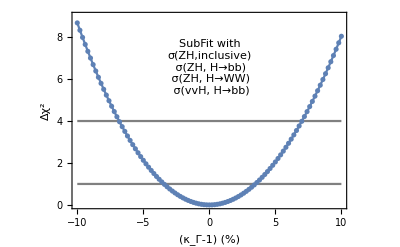

{{x→0.0348282}}

```mathematica
Show[Plot[{Interpolation[tempdata][x/100],1,4},{x,-0.1*100,0.1*100},PlotRange->{0,9},Frame->True,FrameLabel->{"(κ_Γ-1) (%)","Δχ^2"},BaseStyle->16,PlotStyle->{Automatic,Gray,Gray}],ListPlot[{#[[1]]*100,#[[2]]}&/@tempdata],Epilog->Inset[Framed[Style["SubFit with\nσ(ZH,inclusive)\n σ(ZH, H→bb)\n σ(ZH, H→WW)\n σ(vvH, H→bb)",13],FrameStyle->None,Background->White],Scaled[{0.5,0.72}]]]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

```mathematica
1/Sqrt[1/3.5^2+1/5.4^2]
```

2.93704

## Tests

```mathematica
chisquare=(x^2/z)^2/dx^2+(y^2/z)^2/dy^2+x^4/dxp^2
```

x^4/dxp^2+x^4/(dx^2 z^2)+y^4/(dy^2 z^2)

```mathematica
{{D[chisquare,x,x],D[chisquare,x,y],D[chisquare,x,z]},
{D[chisquare,y,x],D[chisquare,y,y],D[chisquare,y,z]},
{D[chisquare,z,x],D[chisquare,z,y],D[chisquare,z,z]}}/2/.{x->1,y->1,z->1};
%//MatrixForm
```

(1/2 (12/dx^2+12/dxp^2) | 0 | -4/dx^2
0 | 6/dy^2 | -4/dy^2
-4/dx^2 | -4/dy^2 | 1/2 (6/dx^2+6/dy^2))

```mathematica
Inverse[%658]//Simplify;
%//MatrixForm
```

((dx^2 dxp^2 (dx^2+9 dy^2))/(6 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (4 dx^2 dxp^2 dy^2)/(3 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (2 dx^2 dxp^2 dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))
(4 dx^2 dxp^2 dy^2)/(3 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (dy^2 (9 dx^4+dxp^2 dy^2+9 dx^2 (dxp^2+dy^2)))/(6 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (2 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))
(2 dx^2 dxp^2 dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)) | (2 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)) | (3 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)))

## 7-kappa deriving width for a random request from a senior member (really wasting time)

```mathematica
NSolve[kh[kz,kw,kg,kgamma,kb,kt,ktau]kappah==1,kb]
```

{{kb→-1/(√kappah)7.3035×10^-9 √(3.241×10^16-7.746×10^12 kappah-2.7743×10^15 kappah kg^2-7.45431×10^13 kappah kgamma^2-8.68589×10^14 kappah kt^2-2.07168×10^15 kappah ktau^2-7.00057×10^15 kappah kw^2-8.65348×10^14 kappah kz^2)},{kb→1/(√kappah)7.3035×10^-9 √(3.241×10^16-7.746×10^12 kappah-2.7743×10^15 kappah kg^2-7.45431×10^13 kappah kgamma^2-8.68589×10^14 kappah kt^2-2.07168×10^15 kappah ktau^2-7.00057×10^15 kappah kw^2-8.65348×10^14 kappah kz^2)}}

```mathematica
Module[{kappah},kappah=0.95;NMinimize[{chisquarecepc[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}]]
```

{4.82534,{kz→0.999106,kg→1.02916,kgamma→1.02834,kw→1.0274,kt→1.03051,ktau→1.02792}}

```mathematica
widthdata70=Table[{kappah,NMinimize[{chisquarecepc[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}][[1]]},{kappah,0.95,1.05,0.005}]
```

{{0.95,4.82534},{0.955,3.87901},{0.96,3.04191},{0.965,2.31162},{0.97,1.68578},{0.975,1.16209},{0.98,0.738316},{0.985,0.412298},{0.99,0.181927},{0.995,0.0451574},{1.,8.65073×10^-11},{1.005,0.0445222},{1.01,0.176845},{1.015,0.395143},{1.02,0.69764},{1.025,1.08261},{1.03,1.54838},{1.035,2.0933},{1.04,2.71581},{1.045,3.41435},{1.05,4.18742}}

```mathematica
NSolve[Interpolation[widthdata70][1+x]==1,{x,1.02}]
```

NSolve::ivar: 1.02 is not a valid variable.

NSolve[InterpolatingFunction[…][1+x]==1,{x,1.02}]

```mathematica
widthdata70L=Table[{kappah,NMinimize[{chisquarecepcL[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}][[1]]},{kappah,0.95,1.05,0.005}]
```

{{0.95,8.13819},{0.955,6.54393},{0.96,5.13311},{0.965,3.90178},{0.97,2.84613},{0.975,1.96245},{0.98,1.2471},{0.985,0.696577},{0.99,0.307432},{0.995,0.0763258},{1.,1.32684×10^-13},{1.005,0.0752819},{1.01,0.29908},{1.015,0.668383},{1.02,1.18026},{1.025,1.83184},{1.03,2.62034},{1.035,3.54305},{1.04,4.59732},{1.045,5.78057},{1.05,7.09028}}

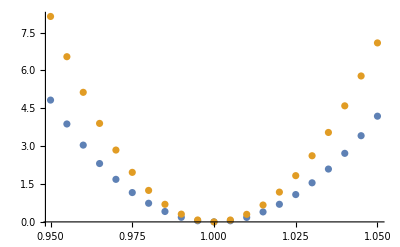

```mathematica
ListPlot[{widthdata70,widthdata70L}]
```

```mathematica
NSolve[Interpolation[widthdata70][1+x]==1,x]
NSolve[Interpolation[widthdata70L][1+x]==1,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.0232213}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.0179354}}

```mathematica
FindRoot[Interpolation[widthdata70][1+x]==1,{x,0}]
FindRoot[Interpolation[widthdata70L][1+x]==1,{x,0}]
```

InterpolatingFunction::dmval: Input value {11.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{x→0.024011}

InterpolatingFunction::dmval: Input value {11.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{x→0.0183896}